## G(T) for p0=3.825

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/p382/";
```

```mathematica
Directory[]
```

/home/chengling

```mathematica
Tlist={0.063, 0.039 ,0.03105 ,0.025, 0.016 ,0.01, 0.008 ,0.0063, 0.005 ,0.00385 ,0.0031 ,0.0028 ,0.0025 ,0.0022 ,0.002 ,0.0018, 0.001, 0.00067 ,0.0005 ,0.0004, 0.00033 };
```

```mathematica
Tstring=ToString[NumberForm[#,{9,8},ExponentFunction->(Null&)]]&/@Tlist
```

{0.06300000,0.03900000,0.03105000,0.02500000,0.01600000,0.01000000,0.00800000,0.00630000,0.00500000,0.00385000,0.00310000,0.00280000,0.00250000,0.00220000,0.00200000,0.00180000,0.00100000,0.00067000,0.00050000,0.00040000,0.00033000}

```mathematica
Length[Tlist]
```

21

```mathematica
spacing={22,22,22,22,22,26,30,221,243,313,360,360,360,360,360,400,400,400,400,400,400};
```

```mathematica
Length[spacing]
```

21

```mathematica
g2[[20/2;;]]
```

{0.195402,0.18489,0.181493,0.178496,0.173882,0.170987,0.169029,0.158645,0.157026,0.154476,0.156472,0.155204}

```mathematica
derivatives=Table[Table[Import[StringJoin[saveFolder,"SigmaSecD_N4096_p3.8250_T",Tstring[[T]],"_Spacing",ToString[spacing[[T]]],"_idx",ToString[i],".nc"],"Data"],{i,0,2}],{T,Length[Tlist]}];
```

```mathematica
g1=Table[Mean[Table[Mean[Normal[derivatives[[T,i,2]]][[Floor[Length[derivatives[[T,i,2]]]/2];;]]]/4096,{i,3}]],{T,Length[Tlist]}]
```

{0.661692,0.531386,0.478027,0.432197,0.351889,0.286573,0.261682,0.239212,0.220844,0.203875,0.192459,0.187836,0.183126,0.178468,0.175394,0.172303,0.160424,0.156111,0.154053,0.153078,0.152482}

```mathematica
g2=Table[Mean[Table[Variance[Normal[derivatives[[T,i,1]]*4096][[Floor[Length[derivatives[[T,i,2]]]/2];;]]],{i,3}]]/4096/Tlist[[T]],{T,Length[Tlist]}]
```

{0.467166,0.401087,0.380038,0.352568,0.296185,0.260019,0.237446,0.2222,0.208179,0.196108,0.184663,0.181055,0.177797,0.172883,0.170868,0.168787,0.15722,0.154561,0.151569,0.154168,0.15174}

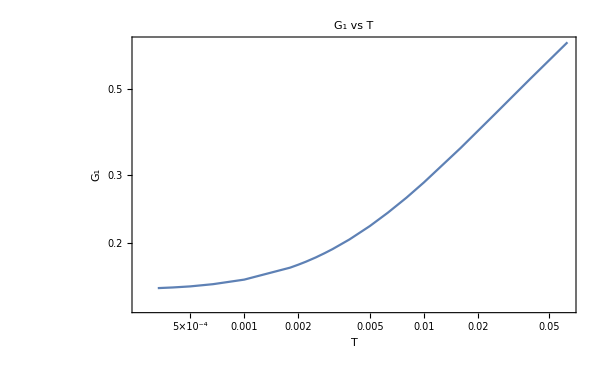

```mathematica
G1Plot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_1"},ImageSize->600,PlotLabel->"G_1 vs T",Joined->True]
```

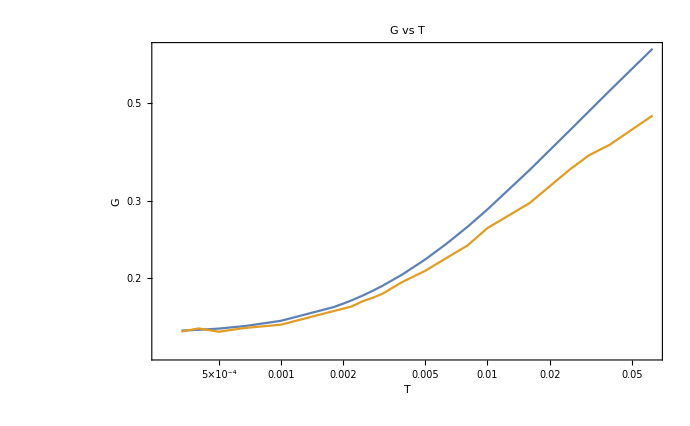

```mathematica
G2Plot=ListLogLogPlot[{Table[{Tlist[[T]],g1[[T]]},{T,Length[Tlist]}],Table[{Tlist[[T]],g2[[T]]},{T,Length[Tlist]}]},FrameLabel->{"T","G"},ImageSize->600,PlotLabel->"G vs T",Joined->True,PlotLabel->{"G_1,G_2"}]
```

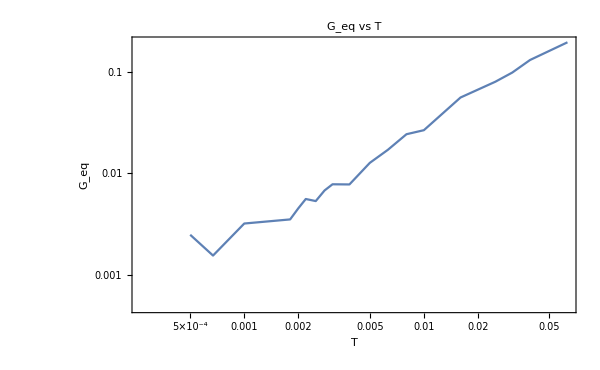

```mathematica
GSFPlot=ListLogLogPlot[Table[{Tlist[[T]],g1[[T]]-g2[[T]]},{T,Length[Tlist]}],FrameLabel->{"T","G_eq"},ImageSize->600,PlotLabel->"G_eq vs T",Joined->True]
```

### G(t)=SACF*β*Area+Geq

```mathematica
data=Import["/home/chengling/Research/Project/Cell/glassyDynamics/N4096/SACtime_N4096_p3.8000_T0.00337100_waitingTime5times464.15_idx2.nc","Data"]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
data[[2,130]]
```

2949.12

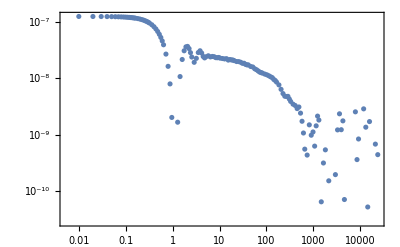

```mathematica
ListLogLogPlot[Table[{data[[2,t]],data[[1,t]]},{t,Length[data[[1]]]}],PlotRange->All]
```